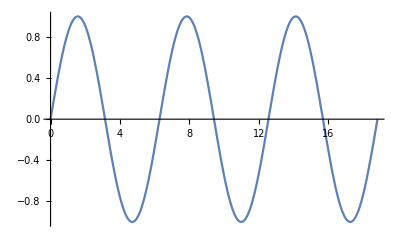

```mathematica
Plot[Sin[x],{x,0,6Pi}]
```

```mathematica
Integrate[Sin[x], {x, 0,Pi}]
```

2

WolframAlphaQueryParseResults

US counties in Washington

WolframAlphaQueryResults

Missing[NotAvailable]

WolframAlphaQueryParseResults

{A finite sequence of n letters from some alphabet is said to be an n-ary word.,A finite sequence of n letters from some alphabet is said to be an n-ary word.}

WolframAlphaQueryResults

1 | verb | determine the number or amount of
2 | verb | have weight; have import, carry weight
3 | verb | show consideration for; take into account
4 | verb | name or recite the numbers in ascending order
5 | verb | put into a group
6 | verb | include as if by counting
7 | verb | have a certain value or carry a certain weight
8 | verb | have faith or confidence in
(12 meanings)

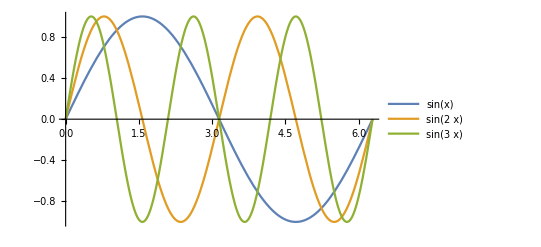

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

```mathematica
Plot[2Sin[x]+x,{x,0,15},Filling->Bottom]
```

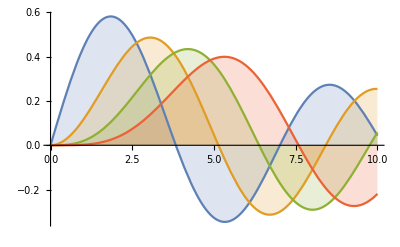

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

```mathematica
Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2}],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}],Green,Opacity[.3],Cuboid[{-2,-2,-2},{2,2,-1}]}]
```

-Graphics3D-

```mathematica
Export["model.stl",Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->"Rainbow",Mesh->None],{"STL","BinaryFormat"-> False}]
```

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->"Rainbow",Mesh->None]
```

-Graphics3D-

```mathematica
Export["rickDemo.stl",Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->"Rainbow",Mesh->None],{"STL","BinaryFormat"-> False}]
```

rickDemo.stl

```mathematica
Integrate[(Sin[x]/x), {x, 0, 4*Pi}]
```

SinIntegral[4 π]

```mathematica
Plot3D[Im[ArcSin[(x+I y)^4]],{x,-2,2},{y,-2,2},Mesh->None,PlotStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]],ExclusionsStyle->{None,Red}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[Sin[a x+b],{x,0,6}],{{a,2,"Multiplier"},1,4},{{b,0,"Phase Parameter"},0,10}]
```

```mathematica
Manipulate[ContourPlot[q1/Norm[{x,y}-p[[1]]]+q2/Norm[{x,y}-p[[2]]],{x,-2,2},{y,-2,2},Contours->10],{{q1,-1},-3,3},{{q2,1},-3,3},{{p,{{-1,0},{1,0}}},{-1,-1},{1,1},Locator},Deployed->True]
```

```mathematica
Manipulate[ArrayPlot[Take[data,h,w]],{{data,RandomInteger[{0,1},{10,20}]},ControlType->None},{{h,5},1,10,1},{{w,5},1,20,1},Dynamic[Panel[Grid[Outer[Checkbox[Dynamic[data[[#1,#2]]],{0,1}]&,Range[h],Range[w]]]]]]
```

```mathematica
Manipulate[Plot[Sin[a*x],{x,-2*π,2*π}],{a,0,10}]
```

```mathematica
f[x_]:= Sin[x]
f[π]
```

0

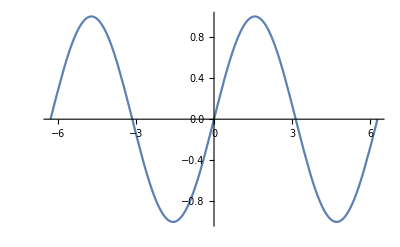

```mathematica
Plot[f[x],{x,-2*π,2*π}]
```

12.4

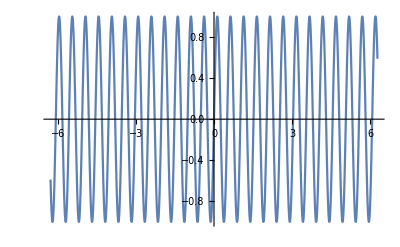

12.4

```mathematica
a = 12.4
Plot[Sin[a*x],{x,-2*π,2*π}]
Manipulate[Plot[Sin[a*x],{x,-2*π,2*π}],{a,-20,20,.1}]
a
```

```mathematica
Manipulate[Factor[x^n-1/x^n],{n,10,100,1}]
```